```mathematica
Exit[]
```

```mathematica
Directory[]
```

/home/rlewis/Dropbox/lean/mm_lean

```mathematica
(* If you are not in the mm_lean directory already,  you should be *)SetDirectory["~/mm_lean"]
```

```mathematica
<<"main.m"
<<"_target/deps/mathematica/lean_form.m"
```

```mathematica
ProveUsingLeanTactic[ForAllTyped[{p,q,r},Prop,Implies[Implies[p,Implies[q,r]],Implies[And[p,q],r]]],"mm_prover"]
```

fun (h : Prop) (h_1 : Prop) (h_2 : Prop) (h_3 : h -> h_1 -> h_2) (h_4 : and h h_1), (h_3 (and.left h h_1 h_4) (and.right h h_1 h_4))

```mathematica
ProveUsingLeanTactic[ForAllTyped[{p,q,r},Prop,Implies[Implies[p,Implies[q,r]],Implies[And[p,q],r]]],"mm_prover",True]
```

LeanLambda[LeanNameMkString["h", LeanNameAnonymous], BinderInfoDefault, LeanSort[LeanZeroLevel], LeanLambda[LeanNameMkString["h_1", LeanNameAnonymous], BinderInfoDefault, LeanSort[LeanZeroLevel], LeanLambda[LeanNameMkString["h_2", LeanNameAnonymous], BinderInfoDefault, LeanSort[LeanZeroLevel], LeanLambda[LeanNameMkString["h_3", LeanNameAnonymous], BinderInfoDefault, LeanPi[LeanNameMkString["a", LeanNameAnonymous], BinderInfoDefault, LeanVar[2], LeanPi[LeanNameMkString["a", LeanNameAnonymous], BinderInfoDefault, LeanVar[2], LeanVar[2]]], LeanLambda[LeanNameMkString["h_4", LeanNameAnonymous], BinderInfoDefault, LeanApp[LeanApp[LeanConst[LeanNameMkString["and", LeanNameAnonymous], LeanLevelListNil], LeanVar[3]], LeanVar[2]], LeanApp[LeanApp[LeanVar[1], LeanApp[LeanApp[LeanApp[LeanConst[LeanNameMkString["left", LeanNameMkString["and", LeanNameAnonymous]], LeanLevelListNil], LeanVar[4]], LeanVar[3]], LeanVar[0]]], LeanApp[LeanApp[LeanApp[LeanConst[LeanNameMkString["right", LeanNameMkString["and", LeanNameAnonymous]], LeanLevelListNil], LeanVar[4]], LeanVar[3]], LeanVar[0]]]]]]]]

```mathematica
<<"natural_deduction_graphs_2.wl"
```

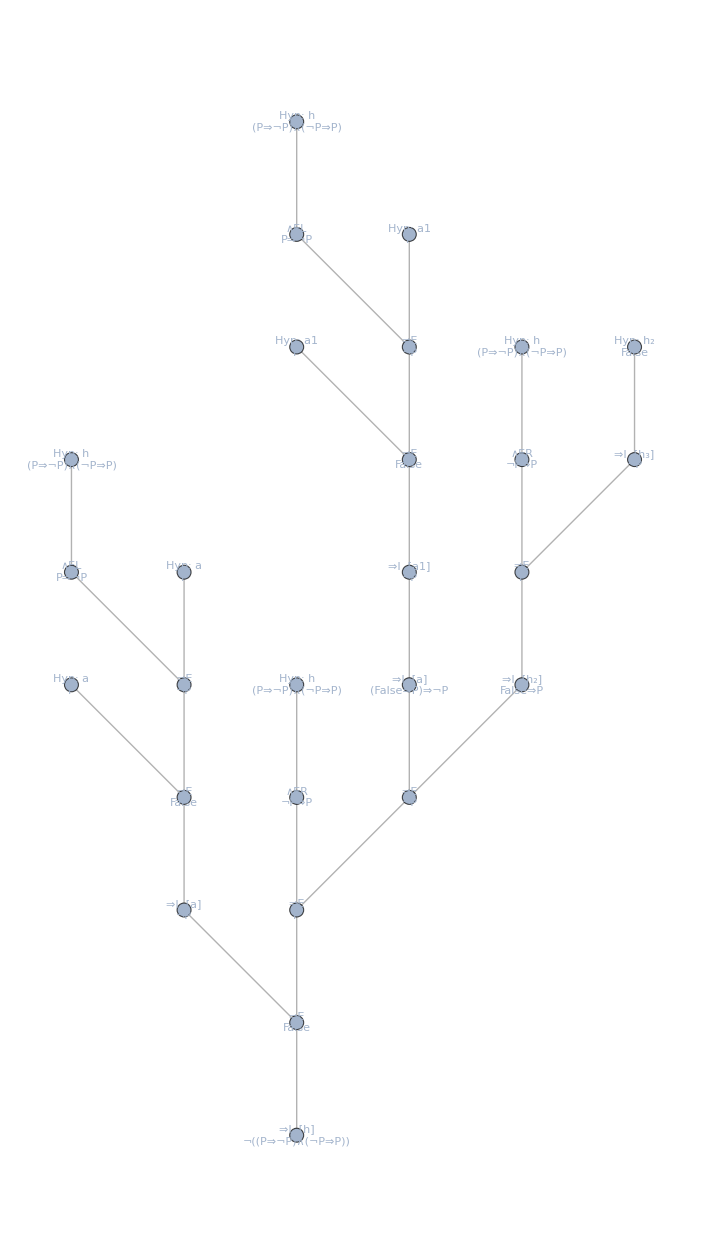

```mathematica
DiagramOfFormula[ForAll[{P},Not[And[Implies[P,Not[P]],Implies[Not[P],P]]]],{P}]
```

```mathematica
<<"CICTranslate.m"
```

```mathematica
RunLeanTactic[LambdaFunction[Alpha,LambdaFunction[Typed[x,Alpha],x]],"elaborate",True]//ToExpression // CICTranslate
```

LambdaFunction[Typed[Alpha,StarType],LambdaFunction[Typed[x,Alpha],x]]

```mathematica
RunLeanTactic[LambdaFunction[Alpha,LambdaFunction[Typed[x,Alpha],x]],"type_check",True]//ToExpression // CICTranslate
```

PiType[Typed[Alpha,StarType],PiType[Typed[x,Alpha],Alpha]]

```mathematica
RunLeanTactic[ForAllTyped[{s,t,u},set[nat],SetUnion[s,SetUnion[t,u]]==SetUnion[SetUnion[u,s],t]],"normalize_set_lemmas"]
```

set.union_comm : ∀ {α : Type ?} (a b : set α), a ∪ b = b ∪ a
set.union_assoc : ∀ {α : Type ?} (a b c : set α), a ∪ b ∪ c = a ∪ (b ∪ c)